## 3d engine rendering algorithm implementation in CRN++

Yaroslav Sergienko (pallada-92@ya.ru)

### Introduction

Here we will implement simplified Ray Marching algorithm as CRN. It is extremely compact 3d engine implementation.
You can read more about this algorithm here: http://jamie-wong.com/2016/07/15/ray-marching-signed-distance-functions/

The CRN, compiled by CRN++, produces correct result, but it is sensitive to error accumulation, so parameters tuning is required.
Best result is produced at large number of iterations, so it takes about 1 min to “render” single pixel with CRN simulation with Mathematica.
For that reason, we are not going to render the whole image (10 000 pixels will take 166 hours) with CRN,
but we can take random pixel and compare CRN result with reference implementation of that algorithm.

There also exists other implementation of the same algorithm in CRN, which is less prone to errors and has much less reactions,
but it has lots of custom optimizations and does not generalize well.

### Reference implementation in Wolfram Language

Here is the “reference” implementation, so we will be able to check, that CRN produces correct result.
We  can also see the result of “rendering” 10 000 pixels.

```mathematica
mat={{0.036,0.555,0.147},{0.853,0,-0.517},{0.737,-0.270,0.302}};
cam ={0.606,0.898,1.243};
rayMarch[pixelX_,pixelY_]:=Module[{n,v=0},
n=mat.{1,pixelX,pixelY};
n=n/Total[n];
Do[v+=Max[Abs[v*n-cam]]-0.3,100];
Clip[(v-1.6)/1.7,{0,1}]
]
Image[Table[rayMarch[pixelX,1-pixelY],{pixelY,0,1,1/100},{pixelX,0,1,1/100}]]
```

-Graphics-

### Run simulation of CRN compiled by CRN++

The idea is to start independent CRN for each pixel.
Pixel coordinates are encoded by initial concentrations of two species.
Result is encoded by “v” species, that concentration should converge to final value after some time.
If the pixel is white (i.e. the ray doesn’t intersect the cube), concentration of “v” should grow infinitely,
otherwise the limit is the pixel brighness (0 - black, 1 - white).

Orange line is the expected result, produced by reference implementation above,
green line is the dynamics of "v" species, which is expected to converge to the orange line.

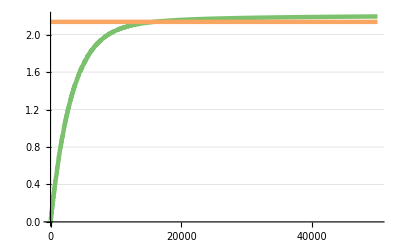

Error = 2.70538%

```mathematica
Get[NotebookDirectory[]<>"3dEngine.m"];

(* Pixel coordinates in range 0..1 *)
pixelX=0.3;
pixelY=0.3;

(* Number of iterations *)
tmax=50000;

(* Speed of result accumulation: the less is better, but it requires to increase tmax *)
fbRate=0.05; 

rsys=rayMarchRsys[pixelX,pixelY,fbRate];
referenceLimit=rayMarch[pixelX,pixelY] * 1.7+1.6;
sol=SimulateRxnsys[ExpandRsys[rsys], tmax];
PlotForPaper[Evaluate[{v[t],referenceLimit}/.sol], tmax,10000]
Print["Error = ",(EvaluateRxnAtPoint[sol,v,tmax]/referenceLimit-1)*100,"%"]
```

### Which combination of fbRate and tmax produces the minimal error

pixelX  pixelY  fbRate  tmax     error
0.3     0.3     1.0     20 000   21%
0.3     0.3     0.9     20 000   20%
0.3     0.3     0.75    20 000   18%
0.3     0.3     0.5     20 000   13%
0.3     0.3     0.2     20 000   7%
0.3     0.3     0.1     50 000   5%
0.3     0.3     0.05    50 000   2.7%